# Giulio

```mathematica
list=Table[x^2,{x,0,10}]
```

{0,1,4,9,16,25,36,49,64,81,100}

```mathematica
Rasterize@ListPlot[list]
```

-Graphics-

```mathematica
Rlist=Table[RandomReal[10,{10,2}],10]
```

{{{8.64817,7.03457},{0.249245,7.81451},{1.26468,2.86088},{0.970228,6.59359},{6.7682,6.11141},{0.051897,4.06512},{9.81377,5.45953},{9.15312,6.78953},{7.98302,7.47721},{7.54762,6.66593}},{{2.41166,8.3365},{9.42061,5.3667},{7.08019,5.45805},{2.49377,0.129898},{7.19684,1.78701},{1.3128,9.14744},{9.40227,3.1002},{5.08141,3.93664},{7.20145,1.55358},{9.36352,8.44073}},{{8.77521,6.43001},{3.15569,6.94614},{9.08992,6.86087},{5.55649,0.102473},{2.18009,4.68107},{5.06305,1.55987},{6.44608,0.671326},{1.41042,1.15634},{3.10823,6.85014},{7.5377,6.38021}},{{4.97811,9.90042},{7.86673,2.6362},{1.88064,8.94954},{2.87435,3.92998},{6.22255,6.36478},{4.4716,1.33338},{6.05446,1.70828},{9.8576,7.5797},{8.00935,9.51293},{3.3273,4.02597}},{{2.36429,1.4536},{8.2576,0.574367},{4.7942,5.50711},{4.12173,0.930802},{2.93963,0.173657},{3.42305,6.58334},{6.49941,0.242267},{7.0816,6.19691},{0.508069,0.968727},{9.8533,6.80541}},{{1.67516,2.70111},{9.51605,3.29758},{1.85992,0.33358},{6.24842,8.91514},{5.96863,9.59687},{6.90035,4.88785},{7.28415,7.54795},{2.26942,9.64749},{7.07974,2.90656},{1.74163,6.16732}},{{2.49765,5.58821},{3.22421,1.35707},{4.88223,4.43506},{6.93541,1.03163},{6.30592,7.73669},{3.55556,4.37888},{8.56089,1.03328},{5.46856,8.61595},{9.75627,2.49381},{1.29424,6.2809}},{{8.97488,9.11011},{4.73649,4.25078},{5.4368,5.80517},{7.21346,4.21192},{1.23819,6.78383},{9.10238,0.718243},{2.34924,0.564117},{8.44275,7.66313},{7.96025,4.68975},{1.60013,4.09491}},{{4.03373,2.15679},{0.378085,6.53978},{9.60095,1.57138},{2.22335,5.98519},{4.65919,7.41265},{2.03926,2.67701},{5.26922,7.22925},{9.04765,4.29144},{5.24148,9.16201},{0.861117,1.28507}},{{6.52843,4.22907},{0.472587,8.94728},{0.13544,6.24541},{2.46971,5.15225},{6.17328,8.91324},{4.4394,9.65421},{7.38613,9.94947},{2.32251,9.43495},{0.576605,1.36741},{3.73465,4.09235}}}

```mathematica
Part[Rlist,4]
```

{{4.97811,9.90042},{7.86673,2.6362},{1.88064,8.94954},{2.87435,3.92998},{6.22255,6.36478},{4.4716,1.33338},{6.05446,1.70828},{9.8576,7.5797},{8.00935,9.51293},{3.3273,4.02597}}

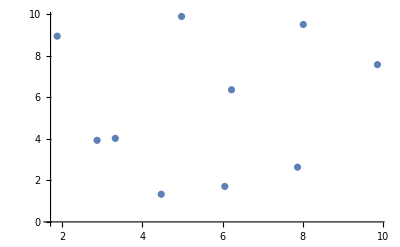

```mathematica
ListPlot[Part[Rlist,4]]
```

```mathematica
AlphaChannel[Rasterize[ListPlot[Part[Rlist,4],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
```

-Graphics-

```mathematica
Binarize[AlphaChannel[Rasterize[ListPlot[Part[Rlist,4],PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0];
```

```mathematica
labels=tr;
```

```mathematica
data=AlphaChannel[Rasterize[ListPlot[Part[Rlist,4],AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
```

-Graphics-

```mathematica
ImageSubtract[labels,data];
```

```mathematica
ImageSubtract[axes,data];
```

```mathematica
background=ColorNegate[ImageAdd[axes,labels,data]];
```

```mathematica
Me
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},226}
 |  |  |  |

```mathematica
GetSegmentation[n_Integer]:=
ImageData[ImageAdd@@MapThread[
ImageMultiply,{Image[{ColorNegate[
ImageAdd[AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],labels=ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0],
AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
],AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]]
],AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0],
AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
],AlphaChannel[Rasterize[ListPlot[Part[Rlist,n],AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]},"Real32"],{0,1,2,3}}
]
]//Round
```

```mathematica
Table[Colorize[GetSegmentation[i]],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dataset[{<|ListPlot[Part[Rlist,1]]->GetSegmentation[1]|>,<|ListPlot[Part[Rlist,2]]->GetSegmentation[2]|>,<|ListPlot[Part[Rlist,3]]->GetSegmentation[3]|>}]
```

Dataset[<>]

```mathematica
MapIndexed[]
```

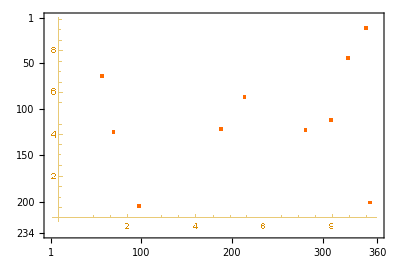

```mathematica
MatrixPlot[%344]
```

```mathematica
GetComponents[2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

{{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},233}
 |  |  |  |

```mathematica
MorphologicalComponents[-Graphics-]
```

```mathematica
(*Evaluate this cell to copy the example input from a cloud object*)
```

```mathematica
ComponentMeasurements[-Graphics-,{"Image","Count","Centroid","StandardDeviation"},All,"Dataset"]
```

Dataset[<>]

```mathematica
MinMax[segmentation]
```

{0,3}

```mathematica
Colorize[segmentation]
```

-Graphics-

```mathematica
plot->segmentation
```

-Graphics-→{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},225}
 |  |  |  |

## Other ideas

```mathematica
plot=ImageRotate[Rasterize[ListPlot[Table[x^2,{x,0,10}]]],0,Background->White]
```

-Graphics-

```mathematica
ImageLines[ColorNegate[plot]]
```

```mathematica
{Line[{{0.,16.76000095879914},{360.,16.760000958799168}}],Line[{{21.979393760619676,226.},{21.22886252403712,0.}}]}
```

{Line[{{0.,16.76},{360.,16.76}}],Line[{{21.9794,226.},{21.2289,0.}}]}

```mathematica
HighlightImage[plot,%]
```

-Graphics-

```mathematica
DominantColors[plot,Automatic,{"Color","CoverageImage"},ColorCoverage->0]
```

{{RGBColor[1., 0.9999994542917262, 0.9999990613752895],-Graphics-},{RGBColor[0.3999997979338314, 0.3999994754160956, 0.39999930595934846],-Graphics-},{RGBColor[0.7019605099695899, 0.7647054401821617, 0.8627441855551392],-Graphics-},{RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783],-Graphics-},{RGBColor[1., 0.8117638099131591, 0.6156855836985293],-Graphics-}}

# Generating Training set

```mathematica
NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

General::mxcacheerr: The cached definitions of the neural networks functionality at /Users/jofre/Library/Caches/Wolfram/PacletCachedData/201904070164/MXNetLink_12.0.0_1agsyq8ky7art appear to be corrupted and will be deleted. If any neural networks functionality doesn't behave as expected, please quit the kernel and try again.

NetGraph[<>]

```mathematica
plots[n_Integer]:=Table[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotRange->{{0,10},{0,10}}]],n]
```

```mathematica
plots[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rasterize@ListPlot[list]
```

```mathematica
rawAxes[n_]:=Table[AlphaChannel[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],n]
```

SetDelayed::write: Tag Image in … is Protected.

$Failed

```mathematica
labels=ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[list,PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0],
axes
]
```

-Graphics-

```mathematica
data=AlphaChannel[Rasterize[ListPlot[list,AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
```

-Graphics-

```mathematica
axes=ImageSubtract[rawAxes,data]
```

-Graphics-

```mathematica
background=ColorNegate[ImageAdd[axes,labels,data]]
```

-Graphics-

```mathematica
MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

```mathematica
MinMax[segmentation]
```

{0,4}

```mathematica
trainingset={1->1.9,2->4.1,3->6.0,4->8.1}
```

```mathematica
testset={3->6.0,4->8.1}
```

```mathematica
trained=NetTrain[LinearLayer[],trainingset,]
```